# Circle-Circle Intersection

### Author

Eric W. Weisstein
September 22, 2007

This notebook downloaded from http://mathworld.wolfram.com/notebooks/PlaneGeometry/Circle-CircleIntersection.nb.

For more information, see Eric's MathWorld entry http://mathworld.wolfram.com/Circle-CircleIntersection.html.

©2007 Wolfram Research, Inc. except for portions noted otherwise

## Area

```mathematica
A[R_,r_,d_]:=r^2 ArcCos[(d^2+r^2-R^2)/(2d r)]+R^2 ArcCos[(d^2+R^2-r^2)/(2d R)]-Sqrt[(-d+r+R)(d+r-R)(d-r+R)(d+r+R)]/2
```

#### v5.2

```mathematica
Integrate[Boole[x^2+y^2<R^2&&(x-d)^2+y^2<r^2],{x,-∞,∞},{y,-∞,∞},Assumptions->r>0&&R>0&&d>0]//Timing
```

{103.445 Second,Piecewise[{{π r^2, (d-r≤0&&d>0&&d+r-R<0)||(d-r>0&&d>0&&d+r-R≤0&&r>0)||(d>0&&d+r-R<0&&r>0)}, {(π R^2)/4, d>0&&d-r==0&&d+r-R==0}, {π R^2, (d-r+R==0&&d>0&&d-r<0)||(d-r+R≤0&&d>0&&d-r<0&&R>0)}, {(2 π r^2 R^2-2 r^2 R √(4 r^2-R^2)+R^3 √(4 r^2-R^2)-R^2 √(4 r^2 R^2-R^4)+8 r^4 ArcCsc[(2 r)/R]-4 r^2 R^2 ArcTan[R^2/(√(4 r^2 R^2-R^4))])/(4 r^2), d>0&&d-r==0&&R>0&&d+r-R>0}, {1/2 (π r^2+π R^2-√(-d^4+2 d^2 r^2-r^4+2 d^2 R^2+2 r^2 R^2-R^4)-2 r^2 ArcTan[(d^2+r^2-R^2)/(√(-d^4-(r^2-R^2)^2+2 d^2 (r^2+R^2)))]-2 R^2 ArcTan[(d^2-r^2+R^2)/(√(-d^4-(r^2-R^2)^2+2 d^2 (r^2+R^2)))]), (d>0&&d-r<0&&d-r+R>0&&d+r-R>0)||(d>0&&d-r>0&&d+r-R>0&&r>0&&d-r-R<0)}, {1/2 r^2 (π+2 ArcTan[d/(√(2 r-R) √R)]+2 ⅈ Log[r]-2 ⅈ Log[d+ⅈ √(2 r-R) √R]), d>0&&d-r<0&&d+r-R==0}}]}

```mathematica
(area=FullSimplify[Integrate[Boole[x^2+y^2<R^2&&(x-d)^2+y^2<r^2],{x,-∞,∞},{y,-∞,∞},Assumptions->r>0&&R>0&&d>0],
r>0&&R>0&&d>0])//Timing//InputForm
```

{14.640000000000015*Second, Piecewise[{{Pi*r^2, d + r < R}, {Pi*R^2, d < r && d + R < r}, 
   {(Sqrt[-((d - r - R)*(d + r - R)*(d - r + R)*(d + r + R))]*(-r^2 + R^2) - d^2*(-2*Pi*r^2 + Sqrt[-((d - r - R)*(d + r - R)*(d - r + R)*(d + r + R))]) - 
      4*d^2*r^2*ArcTan[(d^2 + r^2 - R^2)/Sqrt[-((d - r - R)*(d + r - R)*(d - r + R)*(d + r + R))]])/(4*d^2), 
    (d + r >= R && (d == r || (d < r && d + R > r) || (d > r && d < r + R))) || (d != r && d + r == R)}, 
   {((r - R)*(r + R)*Sqrt[-((d - r - R)*(d + r - R)*(d - r + R)*(d + r + R))] - d^2*(-2*Pi*R^2 + Sqrt[-((d - r - R)*(d + r - R)*(d - r + R)*(d + r + R))]) - 
      4*d^2*R^2*ArcTan[(d^2 - r^2 + R^2)/Sqrt[-((d - r - R)*(d + r - R)*(d - r + R)*(d + r + R))]])/(4*d^2), 
    (d + r > R && (r == d || (d + R > r && d <= r) || (d >= r && d < r + R))) || (d + R == r && d < r)}}, 0]}

```mathematica
(area=FullSimplify[Integrate[Boole[x^2+y^2<R^2&&(x-d)^2+y^2<r^2],{x,-∞,∞},{y,-∞,∞},Assumptions->r>0&&R>0&&d∈Reals],
r>0&&R>0&&d∈Reals])//Timing//InputForm
```

{165.96999999999994*Second, Piecewise[{{Pi*r^2, (d == 0 && r - R < 0) || (d > 0 && d + r - R < 0) || (d < 0 && d - r + R > 0)}, 
   {Pi*R^2, (d == 0 && r - R > 0) || (d > 0 && d - r < 0 && d - r + R < 0) || (d < 0 && d + r > 0 && d + r - R > 0)}, 
   {(2*d^2*Pi*R^2 - d^2*Sqrt[-((d - r - R)*(d + r - R)*(d - r + R)*(d + r + R))] + r^2*Sqrt[-((d - r - R)*(d + r - R)*(d - r + R)*(d + r + R))] - 
      R^2*Sqrt[-((d - r - R)*(d + r - R)*(d - r + R)*(d + r + R))] - 4*d^2*R^2*ArcTan[(d^2 - r^2 + R^2)/Sqrt[-((d - r - R)*(d + r - R)*(d - r + R)*(d + r + R))]])/
     (4*d^2), (d - r == 0 && d > 0 && d + r - R > 0) || (d - r < 0 && d > 0 && d - r + R == 0) || (d - r < 0 && d > 0 && Sqrt[-d^2 + r^2] - R == 0) || 
     (d - r < 0 && d > 0 && d - r + R >= 0 && Sqrt[-d^2 + r^2] - R >= 0) || (d - r <= 0 && d > 0 && d + r - R > 0 && Sqrt[-d^2 + r^2] - R < 0) || 
     (d - r >= 0 && d > 0 && d + r - R > 0 && d - r - R < 0)}, {(d^6 - d^4*r^2 - d^2*r^4 + r^6 - 3*d^4*R^2 - 2*d^2*r^2*R^2 - 3*r^4*R^2 + 3*d^2*R^4 + 3*r^2*R^4 - R^6 + 
      2*d^2*Pi*r^2*Sqrt[-d^4 + 2*d^2*r^2 - r^4 + 2*d^2*R^2 + 2*r^2*R^2 - R^4] - 4*d^2*r^2*Sqrt[-d^4 + 2*d^2*r^2 - r^4 + 2*d^2*R^2 + 2*r^2*R^2 - R^4]*
       ArcTan[(d^2 + r^2 - R^2)/Sqrt[-d^4 - (r^2 - R^2)^2 + 2*d^2*(r^2 + R^2)]])/(4*d^2*Sqrt[-d^4 + 2*d^2*r^2 - r^4 + 2*d^2*R^2 + 2*r^2*R^2 - R^4]), 
    (d + r == 0 && d - r + R <= 0 && d < 0) || (d + r > 0 && d - r + R == 0 && d < 0) || (d + r > 0 && d < 0 && Sqrt[-d^2 + r^2] - R == 0) || 
     (d + r > 0 && d < 0 && Sqrt[-d^2 + r^2] - R >= 0 && d + r - R < 0) || (d + r >= 0 && d - r + R <= 0 && d < 0 && Sqrt[-d^2 + r^2] - R <= 0) || 
     (d + r < 0 && d - r + R == 0 && d < 0) || (d + r <= 0 && d - r + R <= 0 && d < 0 && d + r + R > 0)}, 
   {(d^6 - d^4*r^2 - d^2*r^4 + r^6 - 3*d^4*R^2 - 2*d^2*r^2*R^2 - 3*r^4*R^2 + 3*d^2*R^4 + 3*r^2*R^4 - R^6 + 
      2*d^2*Pi*r^2*Sqrt[-d^4 + 2*d^2*r^2 - r^4 + 2*d^2*R^2 + 2*r^2*R^2 - R^4] + 4*d^2*r^2*Sqrt[-d^4 + 2*d^2*r^2 - r^4 + 2*d^2*R^2 + 2*r^2*R^2 - R^4]*
       ArcTan[(-d^2 - r^2 + R^2)/Sqrt[-d^4 - (r^2 - R^2)^2 + 2*d^2*(r^2 + R^2)]])/(4*d^2*Sqrt[-d^4 + 2*d^2*r^2 - r^4 + 2*d^2*R^2 + 2*r^2*R^2 - R^4]), 
    (d - r == 0 && d + r - R >= 0 && d > 0) || (d - r < 0 && d + r - R == 0 && d > 0) || (d - r < 0 && d > 0 && Sqrt[-d^2 + r^2] - R == 0) || 
     (d - r < 0 && d > 0 && Sqrt[-d^2 + r^2] - R >= 0 && d - r + R > 0) || (d - r <= 0 && d + r - R >= 0 && d > 0 && Sqrt[-d^2 + r^2] - R <= 0) || 
     (d - r > 0 && d + r - R == 0 && d > 0) || (d - r >= 0 && d + r - R >= 0 && d > 0 && d - r - R < 0)}, 
   {(d^6 - 3*d^4*r^2 + 3*d^2*r^4 - r^6 - d^4*R^2 - 2*d^2*r^2*R^2 + 3*r^4*R^2 - d^2*R^4 - 3*r^2*R^4 + R^6 + 
      2*d^2*Pi*R^2*Sqrt[-d^4 + 2*d^2*r^2 - r^4 + 2*d^2*R^2 + 2*r^2*R^2 - R^4] - 4*d^2*R^2*Sqrt[-d^4 + 2*d^2*r^2 - r^4 + 2*d^2*R^2 + 2*r^2*R^2 - R^4]*
       ArcTan[(d^2 - r^2 + R^2)/Sqrt[-d^4 - (r^2 - R^2)^2 + 2*d^2*(r^2 + R^2)]])/(4*d^2*Sqrt[-d^4 + 2*d^2*r^2 - r^4 + 2*d^2*R^2 + 2*r^2*R^2 - R^4]), 
    (d + r == 0 && d < 0 && d - r + R < 0) || (d + r > 0 && d < 0 && d + r - R == 0) || (d + r > 0 && d < 0 && Sqrt[-d^2 + r^2] - R == 0) || 
     (d + r > 0 && d < 0 && d + r - R <= 0 && Sqrt[-d^2 + r^2] - R >= 0) || (d + r >= 0 && d < 0 && d - r + R < 0 && Sqrt[-d^2 + r^2] - R < 0) || 
     (d + r <= 0 && d < 0 && d - r + R < 0 && d + r + R > 0)}, {Integrate[2*Sqrt[r^2 - x^2], {x, -R, R}, Assumptions -> d == 0 && R == r], d == 0 && r - R == 0}}, 0]}

```mathematica
FullSimplify[area,d>0&&r>0&&R>0]
```

Piecewise[{{π r^2, d+r<R}, {π R^2, d<r&&d+R<r}, {((r-R) (r+R) √(-(d-r-R) (d+r-R) (d-r+R) (d+r+R))-d^2 (-2 π R^2+√(-(d-r-R) (d+r-R) (d-r+R) (d+r+R)))-4 d^2 R^2 ArcTan[(d^2-r^2+R^2)/(√(-(d-r-R) (d+r-R) (d-r+R) (d+r+R)))])/(4 d^2), (d+r>R&&(r==d||(d≥r&&d<r+R)||(√(-d^2+r^2)<R&&d≤r)))||(d<r&&(R==√(-d^2+r^2)||d+R==r||(√(-d^2+r^2)≥R&&d+R≥r)))}, {(√(-(d-r-R) (d+r-R) (d-r+R) (d+r+R)) (-r^2+R^2)-d^2 (-2 π r^2+√(-(d-r-R) (d+r-R) (d-r+R) (d+r+R)))-4 d^2 r^2 ArcTan[(d^2+r^2-R^2)/(√(-(d-r-R) (d+r-R) (d-r+R) (d+r+R)))])/(4 d^2), (d+r≥R&&(d==r||(d>r&&d<r+R)||(d<r&&√(-d^2+r^2)≤R)))||(d≠r&&d+r==R)||(d<r&&(√(-d^2+r^2)==R||(√(-d^2+r^2)>R&&d+R>r)))}}]

r inside R

```mathematica
FullSimplify[area,r<R&&d+r<R&&d>0]
```

π r^2

no overlap

```mathematica
FullSimplify[area,d>R+r&&r>0&&R>0]
```

0

Overlapping

```mathematica
FullSimplify[area,0<d<R+r&&r>0&&R>0]
```

Piecewise[{{π r^2, d+r<R}, {π R^2, d<r&&d+R<r}, {((r-R) (r+R) √(-(d-r-R) (d+r-R) (d-r+R) (d+r+R))-d^2 (-2 π R^2+√(-(d-r-R) (d+r-R) (d-r+R) (d+r+R)))-4 d^2 R^2 ArcTan[(d^2-r^2+R^2)/(√((d+r-R) (d-r+R) (-d+r+R) (d+r+R)))])/(4 d^2), (d<r&&(R==√(-d^2+r^2)||d+R==r||(√(-d^2+r^2)≥R&&d+R≥r)))||(d+r>R&&(d≥r||√(-d^2+r^2)<R))}, {(√(-(d-r-R) (d+r-R) (d-r+R) (d+r+R)) (-r^2+R^2)-d^2 (-2 π r^2+√(-(d-r-R) (d+r-R) (d-r+R) (d+r+R)))-4 d^2 r^2 ArcTan[(d^2+r^2-R^2)/(√(-(d-r-R) (d+r-R) (d-r+R) (d+r+R)))])/(4 d^2), True}}]

Tangent

```mathematica
FullSimplify[area,d==-(r+R)&&r>0&&R>0&&d<0]
```

0

```mathematica
FullSimplify[area,d==r+R&&r>0&&R>0&&d==0]
```

Piecewise[{{π r^2, r-R<0}, {π R^2, r-R>0}, {Integrate[2 √(r^2-x^2),{x,-R,R},Assumptions→R==r], True}}]

```mathematica
Integrate[2 √(r^2-x^2),{x,-R,R},Assumptions->R==r]
```

Integrate::idiv: Integral of √R^2 - x^2 does not converge on {-R, R}. More…

Integrate[2 √(r^2-x^2),{x,-R,R},Assumptions→R==r]

```mathematica
Integrate[2 √(r^2-x^2),{x,-R,R},Assumptions->R==r&&(r|R)∈Reals]
```

Integrate::idiv: Integral of √R^2 - x^2 does not converge on {-R, R}. More…

Integrate[2 √(r^2-x^2),{x,-R,R},Assumptions→R==r&&(r|R)∈Reals]

```mathematica
Integrate[2 √(R^2-x^2),{x,-R,R},Assumptions->R>0]
```

π R^2

```mathematica
FullSimplify[area,d==r+R&&r>0&&R>0&&d>0]
```

0

#### v6.0.1

```mathematica
Integrate[Boole[x^2+y^2<R^2&&(x-d)^2+y^2<r^2],{x,-∞,∞},{y,-∞,∞}]//Timing
```

{43.7096,∫_(-∞)^∞ ∫_(-∞)^∞ Boole[x^2+y^2<R^2&&(-d+x)^2+y^2<r^2]ⅆyⅆx}

```mathematica
Integrate[Boole[x^2+y^2<R^2&&(x-d)^2+y^2<r^2],{x,-∞,∞},{y,-∞,∞},Assumptions->r>0&&R>0&&d>0]//Timing
```

{22.757,Integrate[Boole[x^2+y^2<R^2&&(-d+x)^2+y^2<r^2],{x,-∞,∞},{y,-∞,∞},Assumptions→r>0&&R>0&&d>0]}

## Circle-Circle Intersections (Cartesian Coordinates)

```mathematica
circ[1]=Circle@@@{{{-2,0},1},{{2,0},1}};
circ[2]=Circle@@@{{{-1,0},1},{{1,0},1}};
circ[3]=Circle@@@{{{-1/2,0},1},{{1/2,0},1}};
Intersections@@@{circ[1],circ[2],circ[3]}
```

{{Point[{0,-ⅈ √3}],Point[{0,ⅈ √3}]},{Point[{0,0}],Point[{0,0}]},{Point[{0,-(√3)/2}],Point[{0,(√3)/2}]}}

```mathematica
cplot[c_List]:=Module[{pts},
Graphics[{
c,
AbsolutePointSize[6],CircleCenter/@c,
RGBColor[1,0,0],pts=Intersections@@c
},AspectRatio->Automatic,Axes->True,PlotLabel->TraditionalForm/@{0,± (Coordinates/@pts)[[-1,-1]]}]
]
```

```mathematica
Show[GraphicsArray[Table[cplot[circ[i]],{i,3}]],GraphicsSpacing->-.15]
```

Graphics::gptn: Coordinate -ⅈ\ √3 in {0, -ⅈ\ √3} is not a floating-point number.

Graphics::gptn: Coordinate ⅈ\ √3 in {0, ⅈ\ √3} is not a floating-point number.

⁃GraphicsArray⁃

## Radical Line

Rehashing named triangle objects...

```mathematica
rl=Simplify[ToSidelengths[RadicalLine[
circ1=Circle[{alpha1,beta1,gamma1},r1],
circ2=Circle[{alpha2,beta2,gamma2},r2]
]]]
```

TrilinearLine[{1/(b c)(-(b c (b^2 beta1 gamma1+beta1 (-a^2+c^2) gamma1+b c (beta1^2+gamma1^2)))/(a alpha1+b beta1+c gamma1)^2+(b c (b^2 beta2 gamma2+beta2 (-a^2+c^2) gamma2+b c (beta2^2+gamma2^2)))/(a alpha2+b beta2+c gamma2)^2+r1^2-r2^2),1/(a c)(-(a c (a^2 alpha1 gamma1+alpha1 (-b^2+c^2) gamma1+a c (alpha1^2+gamma1^2)))/(a alpha1+b beta1+c gamma1)^2+(a c (a^2 alpha2 gamma2+alpha2 (-b^2+c^2) gamma2+a c (alpha2^2+gamma2^2)))/(a alpha2+b beta2+c gamma2)^2+r1^2-r2^2),1/(a b)(-(a b (a^2 alpha1 beta1+a b (alpha1^2+beta1^2)+alpha1 beta1 (b^2-c^2)))/(a alpha1+b beta1+c gamma1)^2+(a b (a^2 alpha2 beta2+a b (alpha2^2+beta2^2)+alpha2 beta2 (b^2-c^2)))/(a alpha2+b beta2+c gamma2)^2+r1^2-r2^2)}]

```mathematica
lineofcenters=TrilinearLine[Line@@(ctrs=Center/@{circ1,circ2})]
```

TrilinearLine[{-beta2 gamma1+beta1 gamma2,alpha2 gamma1-alpha1 gamma2,-alpha2 beta1+alpha1 beta2}]

```mathematica
pt=Intersections[rl,lineofcenters]
```

{-1/(a b)((alpha2 gamma1-alpha1 gamma2) (-(a b (a^2 alpha1 beta1+a b (alpha1^2+beta1^2)+alpha1 beta1 (b^2-c^2)))/(a alpha1+b beta1+c gamma1)^2+(a b (a^2 alpha2 beta2+a b (alpha2^2+beta2^2)+alpha2 beta2 (b^2-c^2)))/(a alpha2+b beta2+c gamma2)^2+r1^2-r2^2))+1/(a c)((-alpha2 beta1+alpha1 beta2) (-(a c (a^2 alpha1 gamma1+alpha1 (-b^2+c^2) gamma1+a c (alpha1^2+gamma1^2)))/(a alpha1+b beta1+c gamma1)^2+(a c (a^2 alpha2 gamma2+alpha2 (-b^2+c^2) gamma2+a c (alpha2^2+gamma2^2)))/(a alpha2+b beta2+c gamma2)^2+r1^2-r2^2)),1/(a b)(-beta2 gamma1+beta1 gamma2) (-(a b (a^2 alpha1 beta1+a b (alpha1^2+beta1^2)+alpha1 beta1 (b^2-c^2)))/(a alpha1+b beta1+c gamma1)^2+(a b (a^2 alpha2 beta2+a b (alpha2^2+beta2^2)+alpha2 beta2 (b^2-c^2)))/(a alpha2+b beta2+c gamma2)^2+r1^2-r2^2)-1/(b c)(-alpha2 beta1+alpha1 beta2) (-(b c (b^2 beta1 gamma1+beta1 (-a^2+c^2) gamma1+b c (beta1^2+gamma1^2)))/(a alpha1+b beta1+c gamma1)^2+(b c (b^2 beta2 gamma2+beta2 (-a^2+c^2) gamma2+b c (beta2^2+gamma2^2)))/(a alpha2+b beta2+c gamma2)^2+r1^2-r2^2),-1/(a c)((-beta2 gamma1+beta1 gamma2) (-(a c (a^2 alpha1 gamma1+alpha1 (-b^2+c^2) gamma1+a c (alpha1^2+gamma1^2)))/(a alpha1+b beta1+c gamma1)^2+(a c (a^2 alpha2 gamma2+alpha2 (-b^2+c^2) gamma2+a c (alpha2^2+gamma2^2)))/(a alpha2+b beta2+c gamma2)^2+r1^2-r2^2))+1/(b c)((alpha2 gamma1-alpha1 gamma2) (-(b c (b^2 beta1 gamma1+beta1 (-a^2+c^2) gamma1+b c (beta1^2+gamma1^2)))/(a alpha1+b beta1+c gamma1)^2+(b c (b^2 beta2 gamma2+beta2 (-a^2+c^2) gamma2+b c (beta2^2+gamma2^2)))/(a alpha2+b beta2+c gamma2)^2+r1^2-r2^2))}

```mathematica
/.d->Distance@@ctrs
```

```mathematica
eqn1=Distance[{α,β,γ},pt]^2-(4d^2r1^2-(d^2-r1^2+r2^2)^2)/(4d^2);
eqn2=Distance[{α,β,γ},lineofcenters]^2-(4d^2r1^2-(d^2-r1^2+r2^2)^2)/(4d^2);
```

```mathematica
(gb=Factor/@GroebnerBasis[{
Numerator[Together[eqn1]],
Numerator[Together[eqn2]],
a α+b β+c γ-2Area
},{α,β,γ}])//Timing
```

## d = R+r

```mathematica
A[R_,d_]:=R^2 ArcCos[d/R]-d Sqrt[R^2-d^2]
Subscript[d, 1]:=(d^2-r^2+R^2)/(2d)
Subscript[d, 2]:=(d^2+r^2-R^2)/(2d)
```

### a

```mathematica
Factor[4d^2R^2-(d^2-r^2+R^2)^2]
```

-(d-r-R) (d+r-R) (d-r+R) (d+r+R)

```mathematica
Factor[(-d+r-R)(-d-r+R)(-d+r+R)(d+r+R)]
```

-(d-r-R) (d+r-R) (d-r+R) (d+r+R)

```mathematica
%-%%
```

0

### A

```mathematica
A=Simplify[A[R,Subscript[d, 1]]+A[r,Subscript[d, 2]]]
```

1/2 (-2 d √(r^2-((d^2+r^2-R^2)^2)/(4 d^2))+2 r^2 ArcCos[(d^2+r^2-R^2)/(2 d r)]+2 R^2 ArcCos[(d^2-r^2+R^2)/(2 d R)])

```mathematica
Simplify[PowerExpand[Together//@A]]
```

-1/2 √(-d^4-(r^2-R^2)^2+2 d^2 (r^2+R^2))+r^2 ArcCos[(d^2+r^2-R^2)/(2 d r)]+R^2 ArcCos[(d^2-r^2+R^2)/(2 d R)]

```mathematica
Factor[-d^4-(r^2-R^2)^2+2 d^2 (r^2+R^2)]
```

-(d-r-R) (d+r-R) (d-r+R) (d+r+R)

```mathematica
(d-r-R)(d+r-R)(d-r+R)(d+r+R)
```

(d-r-R) (d+r-R) (d-r+R) (d+r+R)

```mathematica
Simplify[A /. d->R+r]
```

0

```mathematica
Simplify[Together//@(Simplify[A /.r->R])]
```

-1/2 d √(-d^2+4 R^2)+2 R^2 ArcCos[d/(2 R)]

### Half Area Overlaps

```mathematica
1/2 (-2 d √(r^2-((d^2+r^2-R^2)^2)/(4 d^2))+2 r^2 ArcCos[(d^2+r^2-R^2)/(2 d r)]+2 R^2 ArcCos[(d^2-r^2+R^2)/(2 d R)])/.{R->1,r->1}//FullSimplify
```

-1/2 d √(4-d^2)+2 ArcCos[d/2]

```mathematica
Solve[-1/2 d √(4-d^2)+2 ArcCos[d/2]==π/2,d]
```

Solve::tdep: The equations appear to involve the variables to be solved for in an essentially non-algebraic way.

Solve[-1/2 d √(4-d^2)+2 ArcCos[d/2]==π/2,d]

```mathematica
Reduce[-1/2 d √(4-d^2)+2 ArcCos[d/2]==π/2&&1/2<d<1,d,Reals]//Timing
```

{23.8135,d==Root[{π-4 ArcCos[#1/2]+#1 √(4-#1^2)&,0.807945506599034418637923480133}]}

```mathematica
d=0.8079455065990344186379234801326308858044719291481968444978`30;
g1=RegionPlot[(x+d/2)^2+y^2<1&&(x-d/2)^2+y^2<1,{x,-1,1},{y,-1,1},PlotStyle->Cyan,Frame->False];
g2=Graphics[{
Circle[{-d/2,0},1],Circle[{d/2,0},1],
PointSize[.02],Point[{{-1,0},{1,0}}d/2]
}];
```

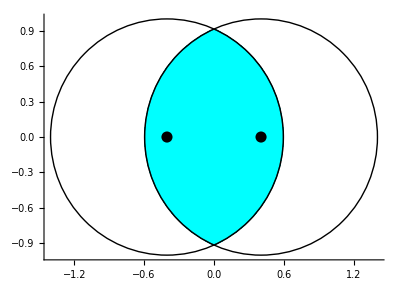

```mathematica
Show[{g1,g2},Axes->True,PlotRange->All,AspectRatio->Automatic]
```

```mathematica
Show[Graphics/@First/@{g1,g2},Axes->True,PlotRange->All,AspectRatio->Automatic]
```

-Graphics-

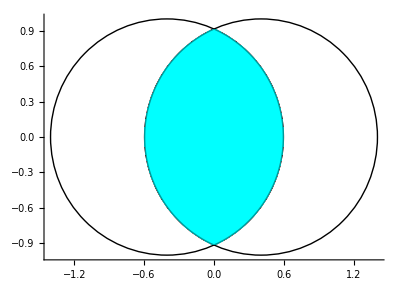

```mathematica
Show[{g2,g1},Axes->True]
```

## Region

```mathematica
Manipulate[RegionPlot[x^2+y^2≤a^2&&(x-c)^2+y^2≤b^2,{x,-2,2},{y,-2,2}],{a,.1,2},{b,.1,2},{c,-1,1}]
```

### Inequality

```mathematica
ineq[x_,y_]:=x^2+y^2≤R^2&&(x-d)^2+y^2≤r^2
```

### Area

```mathematica
Assuming[R>0&&r>0&&d<R+r,Centroid[ineq[x,y],{x,y}]]
```

{(∫_(-∞)^∞ ∫_(-∞)^∞ x Boole[x^2+y^2≤R^2&&(-d+x)^2+y^2≤r^2]ⅆyⅆx)/(∫_(-∞)^∞ ∫_(-∞)^∞ Boole[x^2+y^2≤R^2&&(-d+x)^2+y^2≤r^2]ⅆyⅆx),0}

### Centroid

General::compat: Combinatorica Graph and Permutations functionality has been superseded by preloaded functionaliy. The package now being loaded may conflict with this. Please see the Compatibility Guide for details.

```mathematica
Assuming[a>0&&b>0&&c<a+b,Centroid[ineq[x,y],{x,y}]]
```

$Aborted

```mathematica
Quit
```